```mathematica
(*Plot the bulk and boundary band of Chern Insulator. Created in 2018. *)
```

```mathematica
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
```

```mathematica
H=2 t (Sin[kx]sx+Sin[ky]sy)+(m-2 B (Cos[kx]+Cos[ky]))sz;
```

```mathematica
t=0.2;B=1;m=3B;
```

```mathematica
(*m<4B is non-trivial region*)
```

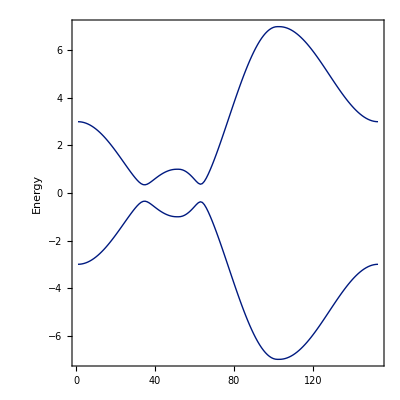

```mathematica
Eig22[k1_,k2_]:=Sort[Eigenvalues[N[H/.{kx->k1,ky->k2}]]]//Chop;
FTB2=ListLinePlot[Join[
Transpose[Table[Eig22[k,0],{k,Pi ,0 ,-Pi/50}]],Transpose[Table[Eig22[k,k],{k,0,Pi,Pi/50}]],
Transpose[Table[Eig22[Pi,k],{k,Pi,0,-Pi/50}]],2],AspectRatio->1,PlotRange->All,PlotStyle->Directive[Thick,RGBColor[0,0.1,0.5]](*RGBColor[0,0.1,0.5]*),Frame->True,FrameLabel->{Automatic,"Energy"},
BaseStyle->{FontFamily->"Times New Roman",FontSize->30}];
Show[FTB2,PlotRange->All]
```

```mathematica
Plot3D[Eig22[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi},BoxRatios->{1, 1, 1},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
H2s[k1_,k2_]:=H/.{kx->k1,ky->k2};

H00[k1_]:=FourierCoefficient[H2s[k1,k2],k2,0];
H01[k1_]:=FourierCoefficient[H2s[k1,k2],k2,1];
H10[k1_]:=FourierCoefficient[H2s[k1,k2],k2,-1];
HF0=H00[k1];
HF1=H01[k1];
HFm1=H10[k1];
```

```mathematica
LL1:=20;(*LL1 is the no of sites in the OBC direction*)hue1=0;hue2=.64;(*colors for left and right edge states*)
eimin=1;eimax=bands LL1;(*range of bands to plot*)
bands=2;
Clear[KK];
KK=ConstantArray[0,{bands LL1,bands LL1}];
For[i=1,i≤LL1,i++,KK[[1+bands (i-1);;bands i,1+bands (i-1);;bands i]]=HF0;]
For[i=1,i≤LL1-1,i++,KK[[1+bands (i-1);;bands i,1+bands i;;bands (i+1)]]=HF1;]
For[i=1,i≤LL1-1,i++,KK[[1+bands i;;bands (i+1),1+bands (i-1);;bands i]]=HFm1;]
```

```mathematica
Clear[Edges];
Edges=Transpose[Table[Sort[Eigenvalues[N[KK/.{k1->kk2}]]],{kk2,-Pi,Pi,Pi/100}]]//Chop;
```

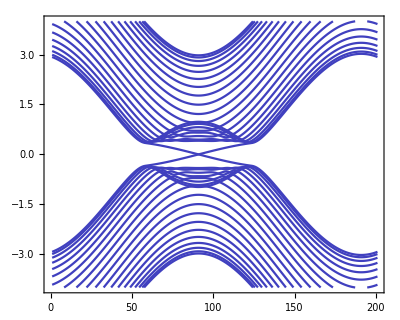

```mathematica
ListPlot[Edges,AspectRatio->0.8,Joined->True,PlotRange->{-4,4},PlotStyle->Blend[{Blue,Gray}],
Frame->True]
```